# Text Analysis of a Real Webpage

Using Nassim Taleb's Opacity notebook as an example.

```mathematica
webpage=Import["https://www.fooledbyrandomness.com/notebook.htm"];
```

```mathematica
contents=TextContents[webpage,VerifyInterpretation->True];
```

Loading Initialization Data...

Loading Initialization Data...

```mathematica
counts=ReverseSort@CountsBy[contents,Type&]
```

Dataset[Association[Person→423,Language→317,Occupation→292,GivenName→262,NonperiodicTiling→214,Country→191,Quantity→182,Religion→152,GovernmentAgency→122,Date→117,Surname→107,Nationality→104,Year→99,PhysicalConstant→96,TopologicalSpaceType→84,Color→76,City→71,Unit→66,OrdinalNumber→60,Organization→58,HistoricalCountry→47,Book→27,Time→24,AstronomicalObjectType→21,SportEvent→16,AdministrativeDivision→15,TropicalStorm→13,Financial→12,Company→11,Food→11,GeographicRegion→11,AstronomicalObject→10,CurrencyAmount→10,FoodManufacturer→9,EthnicGroup→9,Species→8,University→8,Disease→8,Continent→7,Plant→6,Periodical→6,Planet→6,Season→6,Island→5,Element→5,WaterBodyType→5,Ocean→4,FictionalCharacter→3,Building→3,WritingScript→3,Movie→3,Airport→2,Mythology→2,ProgrammingLanguage→2,MeasurementDevice→1,MilitaryConflict→1,Cemetery→1,Neighborhood→1,Protein→1,USState→1,HistoricalEvent→1,FileFormat→1,Mountain→1,Alphabet→1,Gene→1,SportObject→1,PlanetaryMoon→1,PersonTitle→1,MathematicalFunction→1,Mineral→1,DogBreed→1,Cave→1,MusicWork→1,BoardGame→1],TypeSystem`Assoc[TypeSystem`Atom[String],TypeSystem`Atom[Integer],TypeSystem`AnyLength],Association[]]

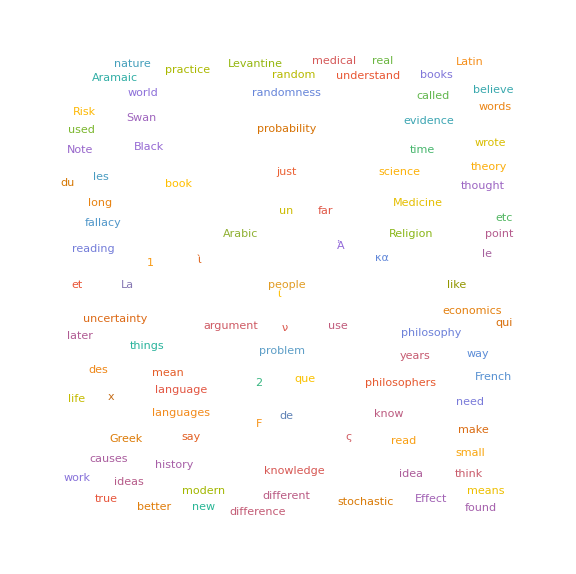

```mathematica
Show[WordCloud[DeleteStopwords[webpage]],ImageSize->Large]
```